```mathematica
(* Student Name *)
(* Date *)
(* MITES Physics III: Intro to Oscillations and Waves *)
(* Understanding Fourier Series*)
```

### (a)

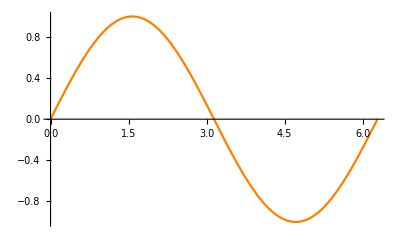

```mathematica
(* Run the code below *)
Plot[ Sin[x],{x,0,2Pi}, PlotStyle -> Orange] (*Plot Sin function *)
```

```mathematica
(* The code below shows how Taylor Series can be used to approximate Trig functions. Run the code, then annotate each line explaining it's meaning in the overall code *)
```



```mathematica
a[n_] := Sin[n Pi/2]/n!; (* Coefficients in the Taylor Series *)

f[n_,x_] := x^(n); (* Polynomial Function of Taylor Series *)

y[x_,nf_]:=Sum[a[n]f[n,x], {n,0, nf}] (* Sum all terms from n=0 to nf *)

Plot[y[x,100],{x,0,2Pi}](* Plot Taylor Series approximation from 0 to 2 Pi*)
```

### (b)

```mathematica
(* Run the code below *)
```

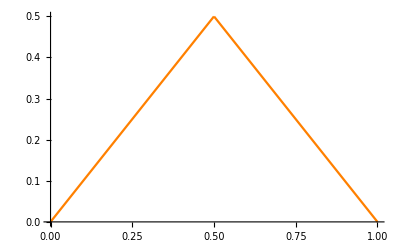

```mathematica
Plot[Piecewise[{{x,x <1/2},{1-x,x>1/2}}],{x,0,1}, PlotStyle -> Orange]
```

```mathematica
(* Modify the first four lines of the Taylor Series code to compute and plot the Fourier Series approximation of the above function *)

(* Create three plots: 1) the first five term in the Fourier Series; 2) the first 10 non-zero terms in the Fourier Series; 3) the first 25 non-zero terms in the Fourier Series*)
```

```mathematica
a[n_] := 4/(n^2 Pi^2) Sin[n Pi/2];  (* Coefficients in the Fourier Series *)

f[n_,x_] :=Sin[n Pi x]; (* Sinusoidal functions in the Fourier Series*)

y[x_,nf_]:=Sum[a[n]f[n,x], {n,1, nf}] (* Sum all terms of Fourier Series up to nf *)
```

### (c)

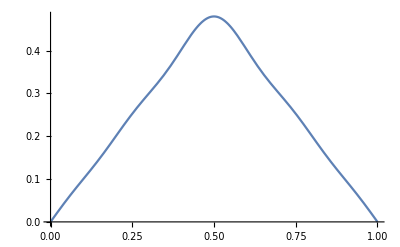

```mathematica
(* i *)
Plot[y[x,10],{x,0,1}](*Plot Fourier Series from 0 to 1; the first five non-zero term*)
```

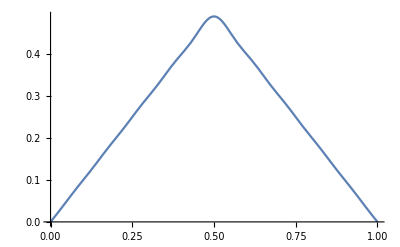

```mathematica
(* ii *)
Plot[y[x,20],{x,0,1}](*Plot Fourier Series from 0 to 1; the first ten non-zero terms*)
```

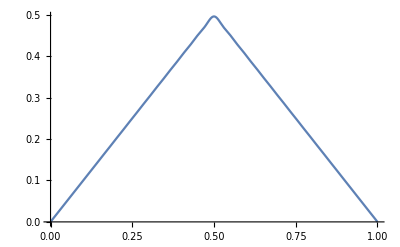

```mathematica
(* iii *)
Plot[y[x,50],{x,0,1}](*Plot Fourier Series from 0 to 1; the first 25 non-zero terms*)
```

### (d)

We note that as we include additional non-zero terms in the series, our Fourier series approaches the original function. So we expect that if we sum an infinite number of terms we exactly reproduce the original function.